Номер 4 :

(1+4 x^2+x^6)^(1/5) Sin[1/18+(2 x)/(√31)+(√(5+x))/7]

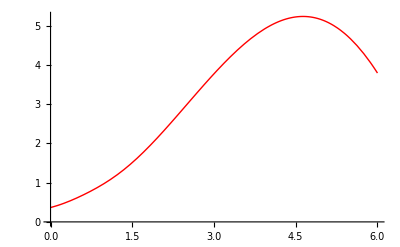

```mathematica
a=0;
b=6;
n=10;
x0=2.4316;
h=(b-a)/n;
f[x_]=(x^6+4 x^2+1)^(1/5)*Sin[(2*x/√31+1/7*√(x+5)+1/18)]
graph = Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

```mathematica
tabl=Table[{a+i* h,f[a+i* h]},{i,0,n}]//N;
TableForm[tabl]
```

0. | 0.366267
0.6 | 0.686507
1.2 | 1.17656
1.8 | 1.90721
2.4 | 2.82599
3. | 3.77226
3.6 | 4.58328
4.2 | 5.10759
4.8 | 5.21258
5.4 | 4.79492
6. | 3.79068

Номер 4 (а)

Для получения кубического сплайна дефекта 1 найдём коэффициенты c_k с помощью встроенной функции LinearSolve.

```mathematica
listC=Table[0,{i,0,n}];
A=Table[0,{n-1},{n-1}];
Do[If[i≠1,A[[i,i-1]]=h];A[[i,i]]=4 h;If[i≠n-1,A[[i,i+1]]=h],{i,1,n-1}]
A//MatrixForm//N
```

(2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4)

Столбец свободных членов:

```mathematica
B=Table[3 ((tabl[[i,2]]-tabl[[i-1,2]])/h-(tabl[[i-1,2]]-tabl[[i-2,2]])/h),{i,3,n+1}]//N;
X=LinearSolve[A,B];
For[i=1,i≤n-1,i++,listC[[i+1]]=X[[i]]];
MatrixForm[listC]
```

(0
0.263273
0.362025
0.293591
0.0313634
-0.189988
-0.398454
-0.60545
-0.674105
-1.05352
0)

Зададим остальные коэффициенты кубического сплайна:

```mathematica
listA=Table[tabl[[i+1,2]],{i,1,n}]
listB=Table[(tabl[[i,2]]-tabl[[i-1,2]])/h+2/3 h listC[[i]]+1/3 h listC[[i-1]],{i,2,n+1}]
listD=Table[(listC[[i]]-listC[[i-1]])/(3 h),{i,2,n+1}]
```

{0.686507,1.17656,1.90721,2.82599,3.77226,4.58328,5.10759,5.21258,4.79492,3.79068}

{0.639042,1.01422,1.40759,1.60256,1.50739,1.15432,0.551982,-0.215752,-1.25233,-1.88444}

{0.146263,0.0548623,-0.0380189,-0.145682,-0.122973,-0.115815,-0.114998,-0.0381419,-0.210786,0.585289}

Теперь зададим кубический сплайн в виде кусочно заданной функции:

```mathematica
sData=Table[{listA[[i]]+listB[[i]] (x-tabl[[i+1,1]])+listC[[i+1]] ((x-tabl[[i+1,1]])^2)+listD[[i]] ((x-tabl[[i+1,1]])^3),tabl[[i,1]]≤x≤tabl[[i+1,1]]}, {i,1,n}]//Simplify

S[x_]=Piecewise[sData]
```

{{0.366267+0.481078 x+0.146263 x^3,0.≤x≤0.6},{0.386009+0.382366 x+0.164521 x^2+0.0548623 x^3,0.6≤x≤1.2},{0.546508-0.0188811 x+0.498893 x^2-0.0380189 x^3,1.2≤x≤1.8},{1.1744-1.06537 x+1.08027 x^2-0.145682 x^3,1.8≤x≤2.4},{0.860469-0.672954 x+0.916769 x^2-0.122973 x^3,2.4≤x≤3.},{0.66719-0.479675 x+0.852343 x^2-0.115815 x^3,3.≤x≤3.6},{0.629079-0.447916 x+0.843521 x^2-0.114998 x^3,3.6≤x≤4.2},{-5.06501+3.61929 x-0.124862 x^2-0.0381419 x^3,4.2≤x≤4.8},{14.0281-8.31388 x+2.36122 x^2-0.210786 x^3,4.8≤x≤5.4},{-111.325+61.3268 x-10.5352 x^2+0.585289 x^3,5.4≤x≤6.}}

Piecewise[{{0.366267+0.481078 x+0.146263 x^3, 0.≤x≤0.6}, {0.386009+0.382366 x+0.164521 x^2+0.0548623 x^3, 0.6≤x≤1.2}, {0.546508-0.0188811 x+0.498893 x^2-0.0380189 x^3, 1.2≤x≤1.8}, {1.1744-1.06537 x+1.08027 x^2-0.145682 x^3, 1.8≤x≤2.4}, {0.860469-0.672954 x+0.916769 x^2-0.122973 x^3, 2.4≤x≤3.}, {0.66719-0.479675 x+0.852343 x^2-0.115815 x^3, 3.≤x≤3.6}, {0.629079-0.447916 x+0.843521 x^2-0.114998 x^3, 3.6≤x≤4.2}, {-5.06501+3.61929 x-0.124862 x^2-0.0381419 x^3, 4.2≤x≤4.8}, {14.0281-8.31388 x+2.36122 x^2-0.210786 x^3, 4.8≤x≤5.4}, {-111.325+61.3268 x-10.5352 x^2+0.585289 x^3, 5.4≤x≤6.}, {0, True}}]

Изобразим полученный кубический сплайн.

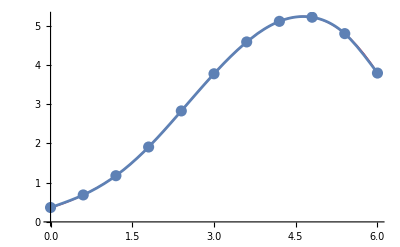

```mathematica
graphD=ListPlot[tabl,PlotStyle->{Darker,PointSize[0.02]}];
graphS=Plot[S[x],{x,a,b}];
Show[graph,graphD,graphS]
```

Номер 4(б):

Интерполируем функцию сплайном с помощью функции Interpolation:

```mathematica
Sf[x_]=Interpolation[tabl,x,Method->"Spline"]
```

InterpolatingFunction[…][x]

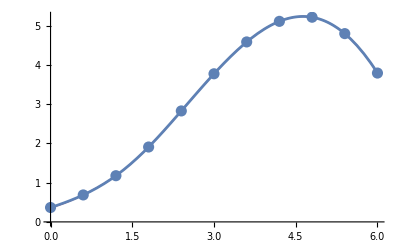

```mathematica
graphSf=Plot[Sf[x],{x,a,b}];
Show[graph,graphD,graphSf]
```

Номер 4(в):
Получим интерполяционный кубический сплайн с помощью функции SplineFit:

```mathematica
Needs["Splines`"]
Spl=SplineFit[tabl,Cubic]
```

SplineFunction[Cubic, {0.,10.}, <>]

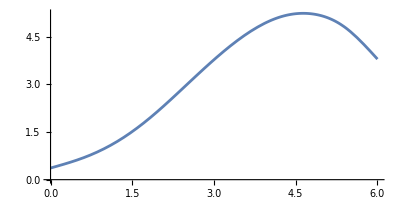

```mathematica
t=(x-a)/h;
graphSpl=ParametricPlot[Spl[t],{t,0,n},AspectRatio->1/2]
```

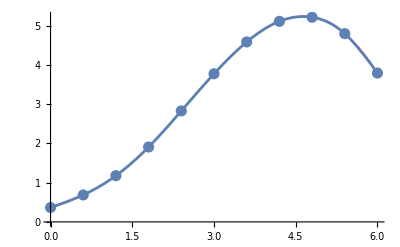

```mathematica
Show[graph,graphD,graphSpl]
```

Номер 4(г):

Значение интерполяционного кубического сплайна в точке x0 :

```mathematica
Print["f[x0]=",f[x0]]
Print["S[x0]=",S[x0]]
```

f[x0]=2.8766

S[x0]=2.87666

Значение интерполирующей функции-сплайна в точке x0:

```mathematica
Print["Sf[x0]=",Sf[x0]]
```

Sf[x0]=2.87665

Значение интерполяционного кубического сплайна, построенного с помощью SplineFit, в точке x0:

```mathematica
Print["Spl[x0]=",Last[Spl[(x0-a)/h]]]
```

Spl[x0]=2.87666